```mathematica
rFunc[invS_]:=√((1/invS)/π);
sFunc[r_]:=N[(π r^2)];
invSFunc[r_]:=1./(π r^2);
```

```mathematica
minTerminalVilliRadius=25mkm;
maxTerminalVilliRadius=80mkm;
maxNonStemVilliRadius=300mkm;
areaFunc[radius_]:=π (radius/mkm)^2;
```

```mathematica
sectionName="2274";

curDir=NotebookDirectory[];
statFile="E:\\06_New cuts of the first sections\\"<>sectionName<>"\\results\\_"<>sectionName<>"_Total_Villous_regions_statistics.csv";



data01=Import[statFile,"Table",FieldSeparators->";"];
dataNames=data01[[1]];
data02=data01[[2;;-1]];
```

```mathematica
data01//Dimensions;
data02//Dimensions;
dataNames
```

{Villous region number,Surface (ÂµmÂ.b2),Perimeter (Âµm),Perimeter_contact (Âµm),Perimeter_frame (Âµm),Nb_IVS_Inside_Region,IVS_Area_Inside_Region (ÂµmÂ.b2),IVS_Perimeter_Inside_Region (Âµm),Nb_Fetal_Capillaries_Inside,Fetal_Capillaries_Area_Inside (ÂµmÂ.b2),FetalCapillariesPerimeter (Âµm)}

```mathematica
areaData=data02[[;;,2]];
perimeterData=data02[[;;,3]];
surfaceDensityData=perimeterData/areaData*1000; (* in mm^-1 *)
```

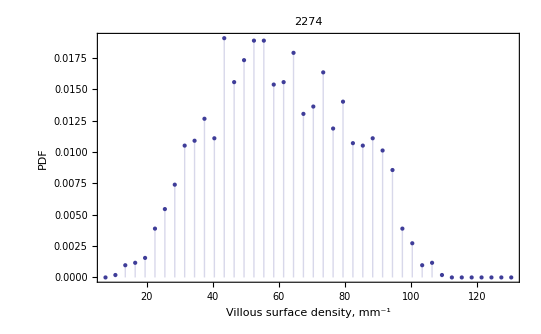

```mathematica
(* Surface density distribution histogram *)
intervalOfInterest={Min[surfaceDensityData]*0.8,Max[surfaceDensityData]*1.2};
selectedSurfaceDensityData=Select[surfaceDensityData,#>=intervalOfInterest[[1]]&&#<=intervalOfInterest[[2]]&];
surfaceDensityBinSize={3};
distribSurfaceDensity=HistogramDistribution[selectedSurfaceDensityData,surfaceDensityBinSize];
pdfSurfaceDensity=PDF[distribSurfaceDensity,s];

pdfSurfaceDensityHistogramPlot=DiscretePlot[pdfSurfaceDensity,{s,intervalOfInterest[[1]],intervalOfInterest[[2]],surfaceDensityBinSize[[1]]},PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{"Villous surface density, mm^-1","PDF"},BaseStyle->{FontSize->20}, PlotLabel->sectionName]
(*Show[pdfSurfaceDensityHistogramPlot,
Graphics[{
{Orange,Line[{{areaFunc[minTerminalVilliRadius],0},{areaFunc[minTerminalVilliRadius],0.0004}}]},
{Darker[Red],Line[{{areaFunc[maxTerminalVilliRadius],0},{areaFunc[maxTerminalVilliRadius],0.0004}}]},
{Darker[Green],Line[{{areaFunc[maxNonStemVilliRadius],0},{areaFunc[maxNonStemVilliRadius],0.0004}}]}
}
]]*)

(* Orange - minimal terminal villus,
Red - maximal terminal villus radius,
Green - maximal stem villus radius *)
```

```mathematica
(* Analyzing correlations between the surface density and the area of a villus *)
```

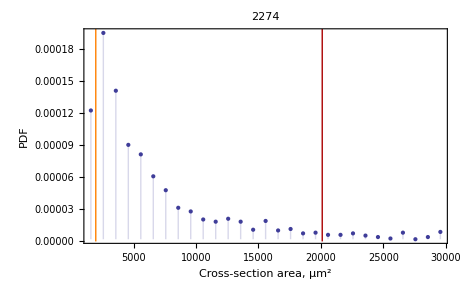

```mathematica
(* Area distribution histogram *)
intervalOfInterest={areaFunc[minTerminalVilliRadius]*0.8,areaFunc[maxTerminalVilliRadius]*1.5};
selectedAreaData=Select[areaData,#>=intervalOfInterest[[1]]&&#<=intervalOfInterest[[2]]&];
areaBinSize={1000};
distribArea=HistogramDistribution[selectedAreaData,areaBinSize];
pdfArea=PDF[distribArea,s];

pdfAreaHistogramPlot=DiscretePlot[pdfArea,{s,intervalOfInterest[[1]],intervalOfInterest[[2]],areaBinSize[[1]]},PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{"Cross-section area, μm^2","PDF"},BaseStyle->{FontSize->20}, PlotLabel->sectionName];
Show[pdfAreaHistogramPlot,
Graphics[{
{Orange,Line[{{areaFunc[minTerminalVilliRadius],0},{areaFunc[minTerminalVilliRadius],0.0004}}]},
{Darker[Red],Line[{{areaFunc[maxTerminalVilliRadius],0},{areaFunc[maxTerminalVilliRadius],0.0004}}]},
{Darker[Green],Line[{{areaFunc[maxNonStemVilliRadius],0},{areaFunc[maxNonStemVilliRadius],0.0004}}]}
}
]]

(* Orange - minimal terminal villus,
Red - maximal terminal villus radius,
Green - maximal stem villus radius *)
```

```mathematica
(* Plotting the histogram of the villous cross-sectional area logarithm *)
```

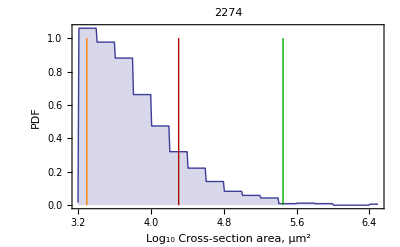

```mathematica
intervalOfInterest={areaFunc[minTerminalVilliRadius]*0.8,∞};
selectedAreaData=Select[areaData,#>=intervalOfInterest[[1]]&&#<=intervalOfInterest[[2]]&];
logAreaData=Log[10,selectedAreaData];
logBinSize=0.2;
distribLogArea=HistogramDistribution[logAreaData,{logBinSize}];
pdfLogArea=PDF[distribLogArea,s];
distribLogAreaTempList=HistogramList[logAreaData,{logBinSize},"PDF"];
binsCenters=Table[(distribLogAreaTempList[[1,i]]+distribLogAreaTempList[[1,i+1]])/2,{i,1,Length[distribLogAreaTempList[[1]]]-1}];
distribLogAreaList=Transpose[{binsCenters,distribLogAreaTempList[[2]]}];

pdfLogAreaHistogramPlot= DiscretePlot[pdfLogArea,{s,Log[10,intervalOfInterest[[1]]],6.5,0.01},PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{"Log_10 Cross-section area, μm^2","PDF"},BaseStyle->{FontSize->20}, PlotLabel->sectionName];

Show[pdfLogAreaHistogramPlot,
Graphics[{
{Orange,Line[{{Log10[areaFunc[minTerminalVilliRadius]],0},{Log10[areaFunc[minTerminalVilliRadius]],1}}]},
{Darker[Red],Line[{{Log10[areaFunc[maxTerminalVilliRadius]],0},{Log10[areaFunc[maxTerminalVilliRadius]],1}}]},
{Darker[Green],Line[{{Log10[areaFunc[maxNonStemVilliRadius]],0},{Log10[areaFunc[maxNonStemVilliRadius]],1}}]}
}
]]

(* Orange - minimal terminal villus,
Red - maximal terminal villus radius,
Green - maximal stem villus radius *)
```